# Squarified Treemap

## A Functional Implementation in Mathematica

By Jeffrey Starr, 2014-02

## Abstract

This paper presents an implementation of the Squarified Treemap algorithm (originally published by Bruls, Huizing, and van Wijk)1 for a single-level of hierarchy written in a functional style using the Mathematica language.

## Introduction

A treemap is a popular visualization technique because of its density (high data content per square inch) and ability to handle hierarchical data. Treemaps visualize quantities by creating rectangles with areas that match (proportionally, at least) the original quantities. Viewers compare values by comparing areas. By using rectangles, treemaps are more dense than pie charts and there is evidence humans can compare areas of rectangles than wedges of a circle. Treemaps can also connote hierarchy by embedding rectangles in other rectangles recursively. This technique is often used to help viewers find files consuming excessive disk space by plotting the file size as the area of the rectangle and embedding the file rectangles within other rectangles to show the directory structure.2

## Rectangle, the Core Data Structure

The Squarified Treemap algorithm draws rectangles in other rectangles. Not all treemap algorithms use rectangles, but rectangles are the most popular choice.

Mathematica provides an existing data structure for a Rectangle which we will use within this paper.

```mathematica
?Rectangle
```

Rectangle[{x_min,y_min},{x_max,y_max}] is a two-dimensional graphics primitive that represents a filled rectangle, oriented parallel to the axes. 
Rectangle[{x_min,y_min}] corresponds to a unit square with its bottom-left corner at {x_min,y_min}.

Note that x and y refer to Cartesian coordinates, not screen coordinates. Beyond this data structure, we need several utility functions:

```mathematica
Coord[side_,Rectangle[{xmin_,ymin_},{xmax_,ymax_}]]:=
Switch[side,
Top,ymax,
Bottom,ymin,
Left,xmin,
Right,xmax]
```

```mathematica
Width[r_Rectangle]:=Abs[Coord[Right,r]-Coord[Left,r]]
```

```mathematica
Height[r_Rectangle]:=Abs[Coord[Top,r]-Coord[Bottom,r]]
```

```mathematica
Area[r_Rectangle]:=Width[r]×Height[r]
```

The aspect ratio of a rectangle is the proportion of the longest edge to the shorter edge (thus, the aspect ratio is always greater than or equal to one). For a degenerate rectangle (where either the height or width is zero), we will define the aspect ratio as infinite.

```mathematica
RectAspectRatio[r_Rectangle]:=
Which[
Width[r]==0∨Height[r]==0,∞,
Width[r]≥Height[r],Width[r]/Height[r],
Width[r]<Height[r],Height[r]/Width[r]
]
```

### Examples: Rectangle Functions

```mathematica
Block[
{r=Rectangle[{0,0},{6,4}]},
{Width[r],Height[r],Area[r],RectAspectRatio[r]}
]
```

{6,4,24,3/2}

## Sidebar: Visualization

The algorithm presented in this paper is independent of a graphical rendering system. However, as we generate rectangles, it is useful to see them plotted for verification. The function below takes a list of rectangles and plots them, with axes and a gridline, using Mathematica’s graphic capabilities.

```mathematica
VisualizeRectangles[rectangles_List]:=
Graphics[
Join[
{EdgeForm[{Thick,Black}],
Opacity[7/10]},
Riffle[rectangles,ColorData["Atoms","ColorList"]]
],
Axes->True,
GridLines->Automatic
]
```

As an example of the output:

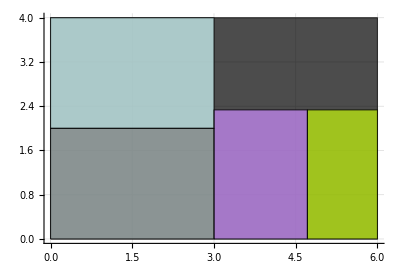

```mathematica
VisualizeRectangles[
{Rectangle[{0,0},{6,4}],
Rectangle[{0,0},{3,2}],
Rectangle[{0,2},{3,4}],
Rectangle[{3,0},{33/7,7/3}],
Rectangle[{33/7,0},{6,7/3}]}]
```

## Filling a Rectangle

## How Many Children?

## Calculating Remaining Space

## Squarify Algorithm

## Dealing with User Data

## References

1	M. Bruls, K. Huizing, and J. van Wijk, "Squarified treemaps," in Proceedings of the Joint Eurographics and IEEE TCVG Symposium on Visualization, pp. 33-42, 2000.

2	http://en.wikipedia.org/wiki/File:Tree_Map.png